```mathematica
Integrate[t t (2t t -rp)2/((2t t -r)^2+rp rp),t]
```

1/4 (4 t+(√2 (-ⅈ r^2+(2+ⅈ) r rp-(1-ⅈ) rp^2) ArcTan[(√2 t)/(√(-r-ⅈ rp))])/(√(-r-ⅈ rp) rp)+(ⅈ √2 (r^2-(1+2 ⅈ) r rp-(1-ⅈ) rp^2) ArcTan[(√2 t)/(√(-r+ⅈ rp))])/(√(-r+ⅈ rp) rp))

```mathematica
FullSimplify[%,{r ∈ Reals,rp ∈ Reals}]
```

1/4 (4 t+(√2 (r-(1-ⅈ) rp) (-ⅈ r+rp) ArcTan[(√2 t)/(√(-r-ⅈ rp))])/(√(-r-ⅈ rp) rp)+(√2 (r-(1+ⅈ) rp) (ⅈ r+rp) ArcTan[(√2 t)/(√(-r+ⅈ rp))])/(√(-r+ⅈ rp) rp))

```mathematica
Integrate[t t /((2t t -r)^2+rp rp),t]
```

(((-ⅈ r+rp) ArcTan[(√2 t)/(√(-r-ⅈ rp))])/(√(-r-ⅈ rp))+((ⅈ r+rp) ArcTan[(√2 t)/(√(-r+ⅈ rp))])/(√(-r+ⅈ rp)))/(4 √2 rp)

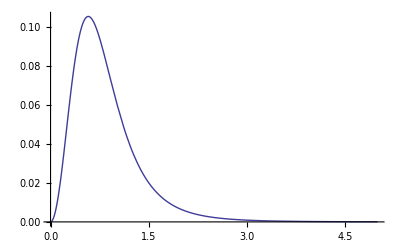

```mathematica
Plot[t^2/(t^2+1)^4,{t,0,5},PlotRange->Full]
```

```mathematica
Integrate[t^2/(t^2+1)^n,{t,0, 1}]
```

(2^-n (-4 n+2^n Hypergeometric2F1[-1/2,n,1/2,-1]))/(3+4 (-2+n) n)

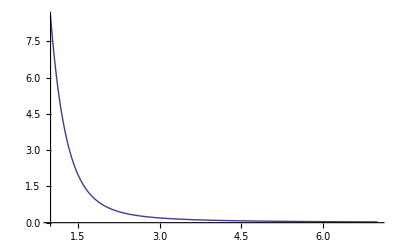

```mathematica
Plot[Integrate[t^2/(t^2+1)^n,{t,0, 10}],{n,1,7},PlotRange->Full]
```

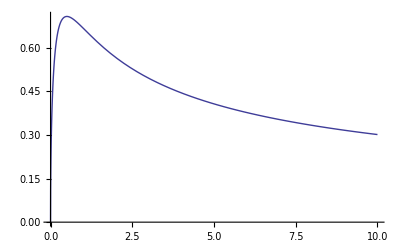

```mathematica
Plot[x^(1/2)/(x+0.5)^(0+1),{x,0,10},PlotRange->Full]
```

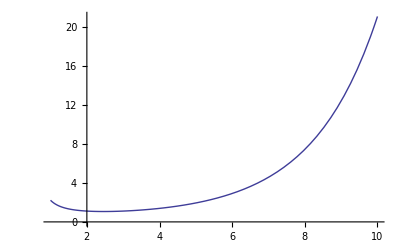

```mathematica
Plot[Integrate[x^(1/2)/(x+0.5)^(n+1),{x,0,Infinity}],{n,1,10}]
```

```mathematica
Integrate[x^(1/2)/(x+1/2)^(0+1),x]
```

2^(1+n) √x (Hypergeometric2F1[1/2,n,3/2,-2 x]-Hypergeometric2F1[1/2,1+n,3/2,-2 x])

```mathematica
l[n_]:=((2(n-1)+1)l[n-1]+1/a^(2(n-1)))/(2(n-1)a^2)
```

```mathematica
l[0]=2/3
```

2/3

```mathematica
l[1]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
Integrate[x^(1/2)/(x+a a)^(4+1),{x,0,1}]
```

If[(Im[a]≥1||1+Im[a]≤0||Re[a]≠0)&&(a^2∉Reals||Re[a^2]≤-1||Re[a^2]≥0),(15 a+55 a^3+73 a^5-15 a^7+15 (1+a^2)^4 ArcCot[a])/(192 a^7 (1+a^2)^4),Integrate[(√x)/((a^2+x)^5),{x,0,1},Assumptions→!((Im[a]≥1||1+Im[a]≤0||Re[a]≠0)&&(a^2∉Reals||Re[a^2]≤-1||Re[a^2]≥0))]]

```mathematica
FullSimplify[%,{n∈Integers,a>0}]
```

(-(1+a^2)^-n+a^(-2 n) Hypergeometric2F1[1/2,n,3/2,-1/a^2])/n

```mathematica
%/.n->0
```

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

```mathematica
D[ArcCot[x],x]
```

-1/(1+x^2)

```mathematica
Simplify[(15 a+55 a^3+73 a^5-15 a^7)/(192 a^7 (1+a^2)^4)]
```

(15+55 a^2+73 a^4-15 a^6)/(192 a^6 (1+a^2)^4)

```mathematica
Factor[15 a+55 a^3+73 a^5-15 a^7]
```

-a (-15-55 a^2-73 a^4+15 a^6)